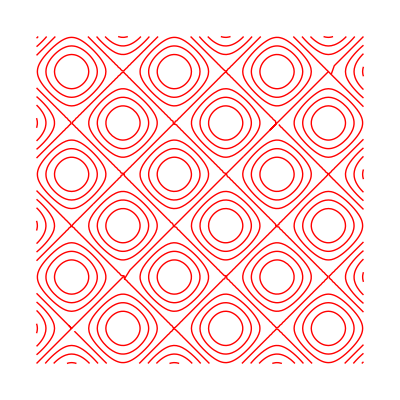
-Graphics3D-
-Graphics-

```mathematica
Printout[f_,a_,b_]:=
Row[{Plot3D[f,{x,a,b},{y,a,b},ImageSize->Scaled[0.875],ColorFunction->"SouthwestColors"],"\n",
ContourPlot[f,{x,a,b},{y,a,b},ImageSize->Scaled[0.875],ContourShading->None,ContourStyle->Red,Frame->None,Axes->None,Ticks->None]}]

Printout[Sin[x]-Sin[y],-10,10]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
f[x_,y_]:=Sin[x^2+y^2]/(x^2+y^2);

TableForm[Table[f[x,y],{x,-1,1,0.25},{y,-1,1,0.25}],TableHeadings->{{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1},{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1}}]//Quiet
```

| -1 | -0.75 | -0.5 | -0.25 | 0 | 0.25 | 0.5 | 0.75 | 1
-1 | 0.454649 | 0.639978 | 0.759188 | 0.822188 | 0.841471 | 0.822188 | 0.759188 | 0.639978 | 0.454649
-0.75 | 0.639978 | 0.802016 | 0.893549 | 0.936156 | 0.948094 | 0.936156 | 0.893549 | 0.802016 | 0.639978
-0.5 | 0.759188 | 0.893549 | 0.958851 | 0.983803 | 0.989616 | 0.983803 | 0.958851 | 0.893549 | 0.759188
-0.25 | 0.822188 | 0.936156 | 0.983803 | 0.997398 | 0.999349 | 0.997398 | 0.983803 | 0.936156 | 0.822188
0 | 0.841471 | 0.948094 | 0.989616 | 0.999349 | Indeterminate | 0.999349 | 0.989616 | 0.948094 | 0.841471
0.25 | 0.822188 | 0.936156 | 0.983803 | 0.997398 | 0.999349 | 0.997398 | 0.983803 | 0.936156 | 0.822188
0.5 | 0.759188 | 0.893549 | 0.958851 | 0.983803 | 0.989616 | 0.983803 | 0.958851 | 0.893549 | 0.759188
0.75 | 0.639978 | 0.802016 | 0.893549 | 0.936156 | 0.948094 | 0.936156 | 0.893549 | 0.802016 | 0.639978
1 | 0.454649 | 0.639978 | 0.759188 | 0.822188 | 0.841471 | 0.822188 | 0.759188 | 0.639978 | 0.454649

```mathematica
g[x_,y_]:=(x^2-y^2)/(x^2+y^2);
h[x_,y_]:=(x y)/(x^2+y^2);
k[x_,y_]:=(x y^2)/(x^2+y^4);
r[x_,y_]:=(y^2 Sin[x]^2)/(x^4+y^4);

TableForm[Table[g[x,y],{x,-1,1,0.25},{y,-1,1,0.25}],TableHeadings->{{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1},{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1}}]//Quiet
```

| -1 | -0.75 | -0.5 | -0.25 | 0 | 0.25 | 0.5 | 0.75 | 1
-1 | 0. | 0.28 | 0.6 | 0.882353 | 1. | 0.882353 | 0.6 | 0.28 | 0.
-0.75 | -0.28 | 0. | 0.384615 | 0.8 | 1. | 0.8 | 0.384615 | 0. | -0.28
-0.5 | -0.6 | -0.384615 | 0. | 0.6 | 1. | 0.6 | 0. | -0.384615 | -0.6
-0.25 | -0.882353 | -0.8 | -0.6 | 0. | 1. | 0. | -0.6 | -0.8 | -0.882353
0 | -1. | -1. | -1. | -1. | Indeterminate | -1. | -1. | -1. | -1.
0.25 | -0.882353 | -0.8 | -0.6 | 0. | 1. | 0. | -0.6 | -0.8 | -0.882353
0.5 | -0.6 | -0.384615 | 0. | 0.6 | 1. | 0.6 | 0. | -0.384615 | -0.6
0.75 | -0.28 | 0. | 0.384615 | 0.8 | 1. | 0.8 | 0.384615 | 0. | -0.28
1 | 0. | 0.28 | 0.6 | 0.882353 | 1. | 0.882353 | 0.6 | 0.28 | 0.

```mathematica
Plot3D[g[x,y],{x,-5,5},{y,-5,5},ImageSize->Scaled[0.875]]
```

-Graphics3D-

```mathematica
Plot3D[h[x,y],{x,-5,5},{y,-5,5},ImageSize->Scaled[0.875]]
```

-Graphics3D-

```mathematica
Plot3D[k[x,y],{x,-5,5},{y,-5,5},ImageSize->Scaled[0.875]]
```

-Graphics3D-

```mathematica
TableForm[Table[r[x,y],{x,-1,1,0.25},{y,-1,1,0.25}],TableHeadings->{{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1},{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1}}]//Quiet
```

| -1 | -0.75 | -0.5 | -0.25 | 0 | 0.25 | 0.5 | 0.75 | 1
-1 | 0.354037 | 0.30256 | 0.166606 | 0.0440824 | 0. | 0.0440824 | 0.166606 | 0.30256 | 0.354037
-0.75 | 0.352954 | 0.413006 | 0.306561 | 0.0906598 | 0. | 0.0906598 | 0.306561 | 0.413006 | 0.352954
-0.5 | 0.216328 | 0.341219 | 0.459698 | 0.216328 | 0. | 0.216328 | 0.459698 | 0.341219 | 0.216328
-0.25 | 0.0609706 | 0.107488 | 0.230433 | 0.48967 | 0. | 0.48967 | 0.230433 | 0.107488 | 0.0609706
0 | 0. | 0. | 0. | 0. | Indeterminate | 0. | 0. | 0. | 0.
0.25 | 0.0609706 | 0.107488 | 0.230433 | 0.48967 | 0. | 0.48967 | 0.230433 | 0.107488 | 0.0609706
0.5 | 0.216328 | 0.341219 | 0.459698 | 0.216328 | 0. | 0.216328 | 0.459698 | 0.341219 | 0.216328
0.75 | 0.352954 | 0.413006 | 0.306561 | 0.0906598 | 0. | 0.0906598 | 0.306561 | 0.413006 | 0.352954
1 | 0.354037 | 0.30256 | 0.166606 | 0.0440824 | 0. | 0.0440824 | 0.166606 | 0.30256 | 0.354037

```mathematica
Plot3D[r[x,y],{x,-5,5},{y,-5,5},PlotRange->All,ImageSize->Scaled[0.875]]
```

-Graphics3D-